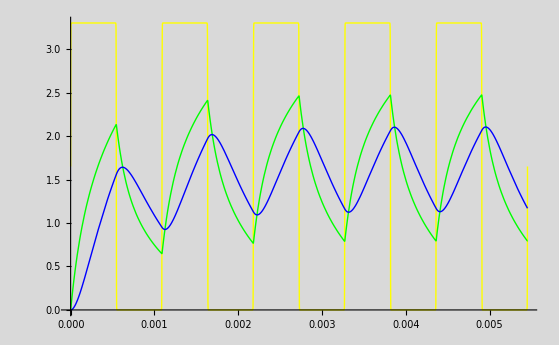

```mathematica
(* Hodnoty soucastek *)
R1=10^4;
R2=10^4;
R3=10^6;
C1=33*10^-9;
C2=22*10^-9;

(* Vstupni hodoty *)
amplituda = 3.3;
frekvence=917;
tmax=1/frekvence*5;
uZ[t_]:=amplituda*(1+Tanh[100 Sin[2*Pi*frekvence*t]])/2;

(* Rovnice uzlu a soucastek *)
proud1=(iR1[t]==iR2[t]+iC1[t]);
proud2=(iR2[t]==iC2[t]+iR3[t]);

odpor1=(uZ[t]-u1[t]==R1*iR1[t]);
odpor2=(u1[t]-u2[t]==R2*iR2[t]);
odpor3=(u2[t]==R3*iR3[t]);

kondik1=(iC1[t]==C1*u1'[t]);
kondik2=(iC2[t]==C2*u2'[t]);


rovnice={proud1, proud2, odpor1, odpor2, odpor3, kondik1, kondik2};
podminky={u1[0]==0, u2[0]==0};
promenne={iR1[t],iR2[t],iR3[t],iC1[t],iC2[t],u1[t],u2[t]};

res=NDSolve[{rovnice, podminky}//Flatten, promenne, {t,0,tmax}];

Plot[{uZ[t],u1[t],u2[t]}/.res//Evaluate,{t, 0, tmax},PlotStyle->{{Thick, Yellow},{Thick, Green},{Thick, Blue}}, Background->LightGray]
```